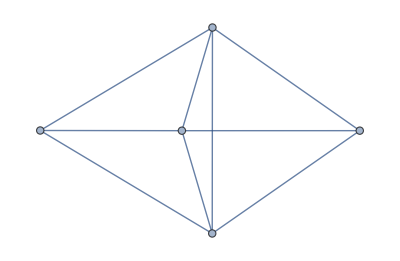

```mathematica
ReadGrof[2]
```

```mathematica
gr=Table[Graph[ReadGrof[k],GraphLayout->"TutteEmbedding"],{k,1,500}];
```

```mathematica
VertexCount[gr[[500]]]
```

11

```mathematica
res=DeleteDuplicates[Select[Flatten[
Table[
Monitor[With[{g=gr[[current]]},Flatten[Table[With[{h=EdgeContract[g,e]},Table[If[IsomorphicGraphQ[h,gr[[m]]],current->m,-1],{m,1,current-1}]],{e,EdgeList[g]}]]],{current,m}],
{current,500,2,-1}
]],#=!=-1&]]
```

{500→211,500→203,500→199,500→268,500→173,500→91,500→296,500→271,500→164,500→165,500→81,500→205,500→240,500→208,499→173,499→290,499→90,499→262,499→270,499→142,499→141,499→204,499→81,499→100,498→148,498→87,498→240,498→81,497→199,497→85,497→268,497→81,497→86,496→276,496→85,496→84,496→81,495→277,495→86,495→242,495→81,494→272,494→84,494→275,494→81,493→240,493→83,493→81,493→274,492→272,492→81,491→273,491→82,491→164,491→81,491→86,491→85,490→107,490→94,490→174,490→261,490→234,490→90,490→89,490→214,490→285,490→80,490→103,490→159,490→97,489→215,489→225,489→107,489→223,489→212,489→232,489→91,489→88,489→208,489→214,489→103,489→80,489→94,489→174,489→108,488→213,488→277,488→174,488→269,488→86,488→80,488→211,488→292,488→84,488→177,487→173,487→290,487→80,487→276,487→291,487→85,487→212,487→200,487→84,487→174,487→176,486→209,486→175,486→80,486→288,486→83,486→210,485→208,485→276,485→174,485→285,485→82,485→80,485→172,484→203,484→290,484→80,484→275,484→84,484→81,484→173,483→99,483→106,483→89,483→196,483→137,483→231,483→79,483→100,483→147,483→96,483→131,483→130,482→170,482→103,482→89,482→173,482→246,482→220,482→79,482→107,482→236,482→140,482→94,482→100,482→109,482→149,482→102,481→169,481→195,481→93,481→168,481→98,481→102,481→79,480→136,480→141,480→92,480→79,480→102,480→248,480→97,480→127,479→146,479→159,479→90,479→230,479→92,479→170,479→79,479→80,479→109,479→93,478→171,478→197,478→91,478→167,478→206,478→151,478→168,478→196,478→147,478→165,478→166,478→79,478→159,478→107,478→123,478→214,477→123,477→189,477→90,477→278,477→135,477→79,477→159,477→261,477→140,477→145,477→89,476→125,476→130,476→87,476→168,476→131,476→79,476→92,475→167,475→191,475→86,475→255,475→260,475→79,475→104,475→143,474→102,474→79,474→105,474→139,474→86,474→130,473→168,473→190,473→83,473→254,473→79,473→105,473→143,472→93,472→138,472→79,472→189,472→247,472→83,472→106,472→130,471→163,471→185,471→85,471→103,471→265,471→79,471→138,470→162,470→182,470→86,470→253,470→79,470→267,470→139,469→147,469→85,469→79,469→252,469→192,469→101,469→144,468→166,468→194,468→83,468→79,468→168,468→193,468→103,468→140,467→165,467→193,467→84,467→79,467→250,467→269,467→103,467→141,466→164,466→192,466→84,466→251,466→79,466→101,466→142,465→160,465→191,465→83,465→86,465→228,465→247,465→100,465→79,464→115,464→138,464→79,464→118,464→260,464→100,464→130,464→143,463→113,463→182,463→82,463→100,463→220,463→79,463→252,463→83,463→101,463→89,462→98,462→103,462→79,462→253,462→102,461→230,461→227,461→98,461→89,461→165,461→281,461→78,461→111,461→136,461→163,461→151,460→93,460→158,460→169,460→78,460→136,460→161,460→125,459→244,459→246,459→136,459→92,459→78,459→151,458→91,458→205,458→164,458→171,458→78,458→161,458→218,457→230,457→203,457→209,457→211,457→227,457→165,457→248,457→170,457→91,457→226,457→225,457→160,457→78,457→207,457→238,457→214,456→113,456→217,456→111,456→88,456→281,456→283,456→161,456→98,456→78,456→162,455→238,455→240,455→168,455→83,455→84,455→250,455→78,454→239,454→242,454→167,454→78,454→83,454→278,453→243,453→276,453→163,453→85,453→165,453→78,452→243,452→268,452→86,452→78,452→283,452→163,451→198,451→277,451→162,451→86,451→165,451→78,450→198,450→199,450→85,450→78,450→283,450→162,449→83,449→274,449→166,449→78,448→242,448→275,448→165,448→84,448→78,448→271,447→242,447→272,447→164,447→84,447→282,447→78,446→241,446→273,446→162,446→82,446→163,446→281,446→78,445→240,445→272,445→81,445→78,445→271,444→168,444→250,444→98,444→79,444→165,444→78,444→161,444→166,444→136,443→78,443→271,443→161,442→209,442→203,442→84,442→242,442→91,442→80,442→282,442→78,442→205,441→239,441→272,441→242,441→240,441→238,441→160,441→78,441→225,440→89,440→97,440→156,440→278,440→77,440→110,440→135,440→153,440→150,439→93,439→158,439→239,439→246,439→151,439→135,439→77,439→124,439→137,438→92,438→135,438→77,438→150,437→91,437→269,437→90,437→159,437→251,437→278,437→79,437→77,437→206,437→80,437→83,437→94,437→175,436→91,436→282,436→123,436→247,436→204,436→136,436→239,436→230,436→142,436→78,436→77,436→90,436→88,435→90,435→258,435→134,435→133,435→77,435→95,434→92,434→148,434→246,434→77,434→137,433→90,433→275,433→158,433→258,433→270,433→137,433→225,433→77,433→97,432→89,432→96,432→152,432→230,432→92,432→82,432→77,432→142,432→87,431→88,431→110,431→282,431→280,431→225,431→151,431→278,431→97,431→77,431→152,430→87,430→137,430→239,430→77,429→85,429→153,429→156,429→77,428→86,428→77,428→279,428→153,427→86,427→152,427→261,427→77,426→85,426→77,426→280,426→152,425→83,425→157,425→77,425→239,424→84,424→156,424→77,424→270,423→84,423→155,423→280,423→77,422→83,422→154,422→77,422→279,421→82,421→152,421→153,421→278,421→77,420→81,420→77,420→270,419→79,419→97,419→261,419→77,419→151,419→157,419→135,418→78,418→151,418→270,418→239,418→77,417→77,417→150,416→77,416→148,416→270,415→78,415→147,415→77,415→278,415→83,415→84,414→79,414→154,414→77,414→245,414→86,414→96,414→92,413→108,413→113,413→217,413→231,413→123,413→160,413→117,413→201,413→149,413→99,413→76,413→119,413→88,413→102,412→170,412→88,412→76,412→89,412→99,412→92,412→96,412→112,412→125,411→99,411→123,411→160,411→136,411→102,411→115,411→125,411→76,411→126,411→127,411→93,411→133,410→123,410→238,410→160,410→244,410→168,410→78,410→76,410→93,410→115,410→87,410→136,410→92,409→160,409→76,409→144,409→125,409→87,409→92,409→148,409→137,408→215,408→217,408→122,408→211,408→91,408→160,408→168,408→173,408→177,408→170,408→196,408→79,408→76,408→146,408→159,408→108,407→207,407→204,407→121,407→203,407→76,407→176,407→146,407→90,407→137,407→158,406→115,406→110,406→246,406→136,406→140,406→127,406→92,406→76,406→135,405→170,405→207,405→76,405→160,405→146,405→120,405→205,405→161,405→91,405→171,405→136,405→123,404→146,404→225,404→123,404→204,404→151,404→136,404→149,404→135,404→133,404→90,404→76,404→145,404→134,404→99,403→120,403→107,403→88,403→244,403→227,403→170,403→136,403→196,403→214,403→109,403→79,403→76,403→121,403→89,403→123,403→98,403→115,403→91,402→111,402→116,402→76,402→225,402→115,402→110,401→100,401→118,401→268,401→102,401→129,401→130,401→85,401→76,400→231,400→117,400→199,400→147,400→155,400→144,400→76,400→148,400→85,399→230,399→89,399→84,399→79,399→142,399→76,399→92,399→87,399→77,399→147,398→232,398→76,398→277,398→162,398→183,398→139,398→86,398→152,397→229,397→114,397→167,397→76,397→192,397→143,397→86,396→116,396→76,396→276,396→163,396→184,396→138,396→85,396→153,395→228,395→118,395→76,395→198,395→168,395→142,395→83,395→154,394→226,394→117,394→272,394→76,394→199,394→164,394→84,394→142,394→155,393→225,393→116,393→275,393→165,393→76,393→200,393→141,393→84,393→156,392→160,392→116,392→76,392→274,392→166,392→193,392→140,392→83,392→157,391→88,391→113,391→164,391→115,391→155,391→129,391→147,391→102,391→125,391→76,391→74,390→214,390→117,390→88,390→273,390→113,390→78,390→89,390→86,390→76,390→112,390→82,390→162,389→217,389→88,389→268,389→160,389→78,389→164,389→79,389→81,389→86,389→76,389→167,388→206,388→114,388→112,388→276,388→88,388→76,388→101,388→96,388→77,388→82,388→153,387→113,387→88,387→167,387→76,387→147,387→115,387→87,387→79,387→143,387→154,387→125,386→217,386→113,386→240,386→164,386→168,386→199,386→198,386→160,386→78,386→76,386→147,385→204,385→112,385→272,385→76,385→85,385→142,385→77,385→137,385→148,384→111,384→116,384→76,384→250,384→98,384→103,384→232,384→102,384→79,384→97,384→115,383→160,383→225,383→111,383→76,383→271,383→161,383→165,383→136,383→78,383→151,382→76,382→110,382→270,382→151,382→156,382→135,382→77,382→150,381→196,381→89,381→104,381→85,381→231,381→79,381→88,381→75,381→96,381→82,381→138,381→100,380→227,380→96,380→155,380→273,380→75,380→89,380→137,380→139,380→148,379→244,379→92,379→75,379→87,379→137,378→207,378→226,378→146,378→165,378→203,378→76,378→78,378→80,378→91,378→141,378→225,378→173,378→75,378→90,378→107,378→149,377→160,377→247,377→93,377→84,377→92,377→75,377→90,377→239,377→102,377→149,376→133,376→135,376→246,376→92,376→75,376→127,375→227,375→204,375→155,375→260,375→149,375→123,375→164,375→271,375→151,375→75,375→91,375→238,375→217,374→149,374→280,374→145,374→142,374→270,374→135,374→90,374→75,374→96,373→115,373→102,373→138,373→227,373→133,373→89,373→167,373→75,373→131,373→124,372→136,372→141,372→75,372→133,372→225,372→76,372→256,372→115,372→135,371→261,371→144,371→84,371→77,371→75,370→260,370→139,370→199,370→85,370→75,369→248,369→75,369→277,369→86,369→139,368→191,368→138,368→268,368→75,368→86,367→141,367→75,367→276,367→85,367→138,366→259,366→143,366→75,366→83,365→258,365→142,365→75,365→84,364→256,364→141,364→275,364→75,364→84,363→75,363→133,363→256,362→238,362→140,362→75,362→274,362→83,361→257,361→137,361→272,361→75,360→227,360→89,360→81,360→164,360→76,360→75,360→137,360→144,360→85,360→79,359→167,359→138,359→139,359→273,359→75,359→82,358→256,358→75,358→272,358→81,357→250,357→79,357→242,357→81,357→78,357→83,357→75,356→249,356→96,356→268,356→75,356→79,356→143,356→137,355→246,355→92,355→81,355→75,355→77,354→225,354→76,354→272,354→78,354→84,354→81,354→75,354→77,353→239,353→87,353→75,353→77,352→204,352→280,352→90,352→84,352→275,352→77,352→75,352→80,352→258,352→149,351→136,351→140,351→75,351→250,351→79,351→248,351→102,351→133,350→238,350→256,350→136,350→75,350→271,350→78,349→75,349→135,349→270,349→77,348→134,348→238,348→244,348→93,348→137,348→74,348→124,348→127,347→159,347→119,347→186,347→243,347→230,347→93,347→88,347→96,347→82,347→74,347→128,347→90,346→123,346→99,346→160,346→78,346→79,346→76,346→75,346→92,346→115,346→93,346→74,346→132,346→125,345→158,345→93,345→238,345→240,345→78,345→75,345→81,345→87,345→74,344→137,344→132,344→240,344→75,344→74,343→89,343→95,343→129,343→241,343→74,343→132,342→135,342→133,342→239,342→87,342→74,341→92,341→132,341→74,340→121,340→186,340→109,340→248,340→209,340→93,340→87,340→91,340→141,340→97,340→80,340→74,340→159,340→119,340→89,339→76,339→142,339→93,339→242,339→132,339→74,339→90,339→77,339→102,339→119,338→127,338→124,338→244,338→92,338→74,338→133,337→89,337→112,337→129,337→139,337→119,337→99,337→164,337→78,337→125,337→74,337→91,337→87,337→113,336→119,336→152,336→134,336→247,336→239,336→127,336→90,336→74,336→96,335→115,335→102,335→128,335→230,335→127,335→89,335→147,335→74,335→141,335→135,334→125,334→131,334→74,334→127,334→160,334→76,334→148,334→115,334→124,333→157,333→130,333→242,333→75,333→74,332→156,332→131,332→83,332→77,332→74,331→155,331→129,331→198,331→85,331→74,330→144,330→74,330→198,330→86,330→129,329→154,329→128,329→243,329→74,329→86,328→131,328→74,328→243,328→85,328→128,327→153,327→128,327→74,327→83,326→152,326→129,326→74,326→84,325→148,325→131,325→242,325→74,325→84,324→74,324→127,324→238,324→75,324→148,323→87,323→130,323→74,323→83,322→74,322→126,322→87,321→151,321→125,321→78,321→77,321→75,321→74,320→150,320→124,320→239,320→74,319→149,319→119,319→240,319→168,319→76,319→137,319→85,319→74,319→131,319→93,318→147,318→128,318→129,318→241,318→74,318→82,317→148,317→74,317→240,317→81,316→135,316→127,316→87,316→74,316→77,315→124,315→126,315→238,315→74,315→75,314→110,314→115,314→239,314→78,314→83,314→77,314→87,314→74,313→96,313→95,313→243,313→74,313→79,313→128,313→132,312→97,312→102,312→242,312→87,312→78,312→84,312→74,311→77,311→74,310→112,310→152,310→119,310→242,310→74,310→80,309→125,309→130,309→74,309→168,309→79,309→144,309→102,309→127,308→87,308→148,308→125,308→74,308→78,307→74,307→124,307→239,307→77,306→73,305→72,305→73,304→69,304→70,304→71,303→69,303→68,302→67,302→71,301→66,300→67,300→70,300→66,300→65,299→65,299→69,299→67,299→70,298→65,298→66,298→69,297→65,297→71,296→64,296→73,296→68,295→63,295→69,294→69,294→61,294→60,293→60,292→68,292→59,292→70,292→61,291→68,291→59,291→71,291→60,290→73,290→68,290→59,289→61,289→60,289→58,289→70,288→59,288→69,288→58,287→65,287→68,287→57,287→64,287→60,287→69,286→65,286→61,286→57,286→69,285→64,285→71,285→70,285→63,285→59,285→57,284→57,284→70,284→63,284→58,283→61,283→68,283→60,283→56,283→63,282→59,282→73,282→64,282→56,281→57,281→64,281→63,281→62,281→56,280→59,280→60,280→55,279→58,279→61,279→55,278→56,278→57,278→55,278→58,278→59,277→59,277→54,277→61,276→59,276→54,276→60,275→73,275→59,275→54,274→54,274→58,273→64,273→60,273→61,273→57,273→54,272→73,272→54,271→54,271→73,271→56,270→54,270→55,269→59,269→71,269→53,268→54,268→60,268→68,268→53,267→61,267→53,267→70,267→52,266→52,265→60,265→53,265→71,265→51,264→69,264→52,264→51,263→61,263→51,262→68,262→51,262→60,261→53,261→59,261→55,261→50,260→53,260→68,260→60,260→50,259→52,259→50,259→58,258→51,258→50,258→59,257→50,257→73,256→50,256→73,256→54,255→57,255→60,255→52,255→67,255→61,255→49,254→49,254→66,254→52,254→58,253→63,253→70,253→53,253→49,252→57,252→69,252→53,252→65,252→49,252→60,251→64,251→51,251→49,251→65,251→69,251→59,250→56,250→59,250→50,250→49,250→58,250→54,249→49,249→68,249→50,249→52,248→50,248→53,248→48,248→59,247→53,247→48,247→51,247→60,246→48,246→54,246→50,246→55,245→49,245→61,245→55,245→48,244→48,244→50,244→47,243→53,243→47,243→60,243→51,242→54,242→53,242→59,242→47,241→57,241→51,241→52,241→47,240→54,240→47,239→47,239→50,239→55,238→50,238→48,238→47,238→54,237→44,237→43,237→52,237→70,237→66,236→43,236→68,236→42,236→60,236→65,236→53,235→45,235→44,235→42,235→70,235→69,235→65,234→42,234→59,234→43,234→51,234→71,234→65,233→26,233→40,233→55,233→45,232→39,232→59,232→63,232→71,232→53,231→42,231→68,231→57,231→60,231→53,231→39,231→54,230→43,230→59,230→49,230→48,230→39,230→51,230→47,230→55,230→57,229→45,229→57,229→39,229→69,229→52,229→61,228→44,228→39,228→61,228→51,228→58,228→49,227→43,227→54,227→64,227→50,227→39,227→60,227→49,227→53,226→42,226→73,226→39,226→68,226→59,226→64,226→51,226→60,225→39,225→73,225→56,225→59,225→50,225→54,225→55,224→46,224→41,224→43,224→38,224→40,223→38,223→59,223→64,223→70,223→42,223→65,222→38,222→61,222→65,222→66,222→43,222→57,222→45,221→38,221→65,221→69,221→63,221→45,221→42,220→38,220→49,220→70,220→57,220→44,220→58,220→65,220→43,219→41,219→57,219→45,219→44,219→51,219→38,219→52,218→38,218→40,218→47,218→57,218→62,218→41,217→38,217→54,217→64,217→49,217→68,217→56,217→39,217→61,217→57,216→46,216→65,216→38,216→45,215→41,215→40,215→49,215→39,215→38,215→46,215→37,215→44,214→41,214→42,214→38,214→53,214→43,214→39,214→63,214→56,214→37,214→57,214→64,213→37,213→59,213→44,213→61,213→70,212→37,212→59,212→42,212→60,212→71,212→73,211→37,211→68,211→43,211→53,211→54,211→42,210→37,210→45,210→69,210→58,209→37,209→59,209→43,209→47,208→40,208→64,208→38,208→60,208→63,208→57,208→37,208→61,208→42,208→44,208→54,207→40,207→37,207→50,207→56,207→39,207→41,207→42,207→72,206→40,206→45,206→37,206→65,206→57,206→49,206→55,206→38,206→59,206→58,206→39,205→37,205→72,205→54,205→40,205→64,205→56,204→37,204→73,204→39,204→60,204→51,204→55,204→50,204→54,203→72,203→73,203→37,203→59,203→54,203→68,202→46,202→36,202→41,201→67,201→52,201→61,201→53,201→35,201→57,201→34,200→59,200→70,200→34,199→54,199→61,199→68,199→34,198→47,198→52,198→61,198→34,197→36,197→42,197→33,197→45,197→67,196→49,196→43,196→34,196→42,196→36,196→57,196→33,196→38,196→50,196→67,196→44,195→35,195→53,195→33,195→34,195→63,194→33,194→71,193→53,193→70,193→34,193→33,193→58,192→53,192→69,192→34,192→33,191→50,191→68,191→33,191→61,190→48,190→61,190→33,190→52,189→49,189→51,189→35,189→32,189→67,189→58,189→33,188→66,188→44,188→53,188→67,188→36,188→63,188→32,188→38,188→52,187→38,187→36,187→64,187→51,187→42,187→65,187→45,187→67,187→32,187→34,187→63,186→67,186→35,186→59,186→64,186→32,185→70,185→33,185→32,185→51,184→70,184→34,184→32,184→60,183→61,183→34,183→71,183→32,182→52,182→33,182→32,182→70,181→69,181→32,180→32,180→68,179→52,179→32,179→61,178→61,178→32,178→60,177→43,177→53,177→66,177→61,177→34,177→44,177→31,177→67,176→31,176→34,176→67,176→60,176→42,176→68,175→43,175→65,175→31,175→58,175→69,175→33,175→45,175→67,174→44,174→59,174→31,174→71,174→32,174→42,174→70,174→67,173→37,173→54,173→44,173→68,173→34,173→31,172→38,172→57,172→44,172→60,172→31,172→67,171→36,171→40,171→30,171→41,170→49,170→37,170→43,170→30,170→48,170→38,170→36,170→39,170→41,169→35,169→30,169→62,168→48,168→47,168→49,168→33,168→34,168→30,167→50,167→53,167→64,167→30,167→33,167→57,166→33,166→58,166→63,166→30,165→53,165→59,165→63,165→34,165→30,165→56,164→53,164→54,164→57,164→34,164→64,164→30,163→51,163→60,163→32,163→30,163→63,162→52,162→61,162→32,162→30,162→63,161→30,161→56,161→62,160→50,160→54,160→53,160→47,160→48,160→39,160→30,159→36,159→53,159→43,159→35,159→49,159→57,159→29,159→38,159→31,159→33,159→67,158→35,158→50,158→54,158→56,158→29,157→33,157→59,157→29,157→50,156→34,156→58,156→29,156→55,155→34,155→61,155→60,155→29,154→33,154→60,154→29,154→61,153→32,153→29,153→58,152→32,152→29,152→59,151→30,151→56,151→55,151→50,151→29,150→29,150→55,149→31,149→54,149→49,149→50,149→60,149→29,149→39,149→34,149→35,148→29,148→54,147→30,147→57,147→29,147→33,147→34,146→41,146→39,146→36,146→30,146→37,146→31,146→28,146→35,145→35,145→55,145→28,144→53,144→34,144→29,144→28,143→52,143→32,143→28,143→33,142→51,142→32,142→28,142→34,141→50,141→33,141→59,141→28,141→34,140→48,140→34,140→28,140→58,140→33,139→53,139→28,139→61,139→32,138→33,138→28,138→60,138→32,137→50,137→29,137→54,137→28,136→48,136→50,136→30,136→28,136→56,135→28,135→29,135→55,134→35,134→50,134→29,134→48,134→27,133→28,133→50,133→27,132→28,132→47,132→27,131→29,131→33,131→53,131→27,131→34,130→28,130→53,130→27,130→33,129→34,129→27,129→52,129→32,128→33,128→27,128→51,128→32,127→28,127→48,127→27,127→29,126→27,126→28,126→48,125→28,125→29,125→30,125→27,124→27,124→50,124→29,123→36,123→50,123→48,123→39,123→56,123→49,123→29,123→35,123→26,123→28,123→30,122→46,122→43,122→38,122→49,122→44,122→66,122→36,122→26,121→40,121→37,121→26,121→50,121→36,121→67,121→35,121→25,121→29,120→41,120→38,120→30,120→40,120→62,120→26,120→48,120→39,120→36,119→31,119→53,119→35,119→47,119→49,119→32,119→26,119→29,119→27,118→44,118→60,118→49,118→26,118→52,118→32,118→33,117→42,117→61,117→57,117→54,117→26,117→34,117→32,116→39,116→59,116→63,116→26,116→58,116→70,116→34,116→33,115→26,115→50,115→30,115→29,115→33,115→39,115→28,115→27,114→45,114→64,114→26,114→69,114→32,113→38,113→57,113→39,113→47,113→49,113→61,113→52,113→30,113→26,112→37,112→54,112→26,112→32,112→29,111→39,111→56,111→62,111→26,111→63,111→30,110→26,110→55,110→56,110→58,110→29,109→36,109→31,109→25,109→48,109→43,109→28,109→35,109→27,108→46,108→42,108→36,108→39,108→38,108→31,108→25,108→67,107→38,107→44,107→33,107→63,107→36,107→25,107→50,107→31,107→42,107→26,107→41,107→49,107→37,106→67,106→60,106→33,106→35,106→25,105→66,105→25,105→61,105→32,105→49,105→33,104→67,104→68,104→25,104→64,104→32,103→49,103→71,103→34,103→25,103→70,103→33,103→63,102→25,102→53,102→28,102→34,102→27,102→30,102→49,101→65,101→34,101→25,101→69,101→32,101→57,100→44,100→68,100→25,100→60,100→32,100→33,100→39,99→36,99→39,99→30,99→26,99→35,99→28,99→27,99→25,98→49,98→63,98→30,98→25,98→62,97→25,97→59,97→29,97→56,96→49,96→32,96→29,96→60,96→28,96→25,95→25,95→51,95→27,94→38,94→71,94→31,94→25,94→55,94→65,93→35,93→47,93→48,93→30,93→28,93→24,93→27,92→28,92→29,92→48,92→24,91→43,91→37,91→34,91→53,91→31,91→36,91→64,91→56,91→30,91→24,91→40,91→47,91→38,90→31,90→59,90→35,90→51,90→55,90→28,90→39,90→24,90→25,89→26,89→25,89→32,89→43,89→28,89→57,89→24,89→34,89→29,88→38,88→26,88→64,88→60,88→39,88→30,88→57,88→25,88→24,88→32,87→29,87→28,87→47,87→24,86→61,86→32,86→53,86→24,85→34,85→24,85→60,85→32,84→54,84→34,84→59,84→24,83→47,83→33,83→24,83→58,82→57,82→32,82→24,81→54,81→24,80→37,80→59,80→31,80→24,79→30,79→33,79→24,79→49,79→53,79→25,79→28,78→47,78→54,78→30,78→24,78→56,77→24,77→29,77→55,76→39,76→26,76→54,76→30,76→34,76→28,76→24,76→29,75→50,75→28,75→54,75→24,74→29,74→27,74→47,74→24,73→22,72→21,72→22,71→16,70→17,70→16,69→23,69→17,69→16,68→16,68→22,67→20,67→16,67→17,67→19,67→15,66→15,66→17,65→20,65→16,65→15,65→23,64→20,64→22,64→14,64→16,63→14,63→16,63→17,62→14,61→16,61→13,61→17,60→16,60→13,59→22,59→16,59→13,58→13,58→17,57→20,57→16,57→17,57→14,57→13,56→13,56→22,56→14,55→13,54→22,54→13,53→13,53→16,53→12,52→17,52→12,51→16,51→12,50→12,50→22,50→13,49→14,49→16,49→12,49→15,49→17,49→13,48→12,48→13,47→13,47→12,46→18,46→15,46→11,45→11,45→20,45→23,45→17,44→11,44→17,44→16,44→15,43→11,43→13,43→20,43→12,43→16,43→15,42→11,42→22,42→16,42→20,41→18,41→11,41→12,41→14,41→21,40→11,40→21,40→13,40→18,40→20,40→14,39→11,39→22,39→14,39→16,39→12,39→13,38→18,38→13,38→20,38→15,38→16,38→14,38→11,38→17,37→21,37→22,37→11,37→16,37→13,36→18,36→11,36→14,36→12,36→15,36→19,36→10,35→19,35→12,35→13,35→14,35→10,34→13,34→17,34→16,34→10,33→12,33→16,33→10,33→17,32→17,32→10,32→16,31→11,31→13,31→15,31→16,31→10,31→19,30→12,30→13,30→14,30→10,29→10,29→13,28→12,28→10,28→13,27→10,27→12,26→11,26→13,26→14,26→17,26→10,25→15,25→16,25→10,25→14,24→13,24→10,23→9,22→8,21→7,21→8,20→9,20→6,20→8,19→6,19→5,18→6,18→7,18→5,17→9,17→5,16→9,16→5,16→8,15→6,15→9,15→5,14→6,14→8,14→5,13→8,13→5,12→5,12→8,11→7,11→8,11→6,11→9,11→5,10→5,9→3,8→3,7→4,7→3,6→3,6→4,5→3,4→2,3→2,2→1}

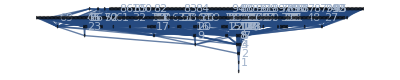

```mathematica
mapped=Graph[res,GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Table[k->Tooltip[k,gr[[k]]],{k,100}], ImageSize->1000,EdgeShapeFunction->"Line"]
```

```mathematica
Sort[Select[Table[{v,VertexInDegree[mapped,v], VertexCount[gr[[v]]]},{v,VertexList[mapped]}],#[[2]]≠0&],#1[[3]]<#2[[3]]&]//DeleteDuplicates
```

{{1,1,4},{2,2,5},{4,2,6},{3,5,6},{5,10,7},{6,6,7},{7,3,7},{8,8,7},{9,6,7},{10,13,8},{11,13,8},{18,5,8},{12,16,8},{13,26,8},{14,15,8},{15,11,8},{19,4,8},{20,9,8},{23,3,8},{17,17,8},{16,26,8},{21,4,8},{22,11,8},{24,20,9},{25,21,9},{27,19,9},{28,32,9},{29,35,9},{30,31,9},{31,17,9},{32,38,9},{33,36,9},{34,37,9},{35,19,9},{36,18,9},{37,21,9},{38,27,9},{41,12,9},{46,6,9},{39,30,9},{40,12,9},{26,20,9},{45,13,9},{42,20,9},{43,20,9},{44,18,9},{47,22,9},{48,21,9},{49,33,9},{50,36,9},{51,23,9},{52,22,9},{53,38,9},{54,39,9},{55,22,9},{62,7,9},{56,22,9},{57,34,9},{58,23,9},{59,41,9},{60,39,9},{61,35,9},{63,22,9},{64,22,9},{65,21,9},{66,10,9},{67,21,9},{68,24,9},{71,15,9},{70,22,9},{69,21,9},{72,4,9},{73,15,9},{132,6,10},{128,7,10},{186,2,10},{249,1,10},{257,1,10},{259,1,10},{256,5,10},{75,40,10},{74,43,10},{184,1,10},{114,2,10},{229,1,10},{183,1,10},{129,8,10},{116,5,10},{120,2,10},{121,3,10},{122,1,10},{126,3,10},{112,6,10},{119,8,10},{76,40,10},{201,1,10},{117,4,10},{245,1,10},{154,5,10},{155,7,10},{157,4,10},{279,2,10},{280,5,10},{152,9,10},{95,3,10},{133,10,10},{134,4,10},{258,4,10},{124,8,10},{150,5,10},{153,7,10},{110,6,10},{77,44,10},{156,6,10},{241,3,10},{282,4,10},{198,6,10},{243,6,10},{239,14,10},{283,3,10},{217,6,10},{238,11,10},{207,4,10},{226,3,10},{218,1,10},{244,6,10},{161,7,10},{158,5,10},{111,5,10},{78,40,10},{281,3,10},{227,7,10},{113,8,10},{118,3,10},{115,15,10},{228,2,10},{160,16,10},{251,2,10},{250,6,10},{193,3,10},{194,1,10},{144,7,10},{101,4,10},{192,3,10},{252,2,10},{267,1,10},{253,2,10},{182,2,10},{162,7,10},{265,1,10},{185,1,10},{163,6,10},{247,5,10},{138,9,10},{254,1,10},{190,1,10},{139,8,10},{105,2,10},{143,7,10},{104,2,10},{260,4,10},{255,1,10},{191,3,10},{125,13,10},{145,3,10},{135,15,10},{278,7,10},{189,2,10},{123,11,10},{166,5,10},{151,12,10},{206,3,10},{167,8,10},{197,1,10},{171,3,10},{230,8,10},{146,6,10},{127,12,10},{248,5,10},{92,20,10},{136,16,10},{98,7,10},{168,13,10},{93,15,10},{195,1,10},{169,2,10},{102,17,10},{149,9,10},{109,4,10},{140,7,10},{236,1,10},{220,2,10},{246,7,10},{170,7,10},{130,9,10},{131,8,10},{96,12,10},{147,11,10},{79,40,10},{231,4,10},{137,16,10},{196,5,10},{106,2,10},{99,7,10},{172,1,10},{210,1,10},{288,1,10},{175,2,10},{209,4,10},{176,2,10},{200,2,10},{291,1,10},{177,2,10},{292,1,10},{269,3,10},{213,1,10},{108,3,10},{88,14,10},{232,3,10},{212,2,10},{223,1,10},{225,12,10},{215,2,10},{97,9,10},{159,8,10},{103,8,10},{80,14,10},{285,2,10},{214,6,10},{89,20,10},{234,1,10},{261,5,10},{174,5,10},{94,4,10},{107,6,10},{82,12,10},{273,5,10},{274,4,10},{83,23,10},{275,7,10},{272,10,10},{242,12,10},{277,5,10},{84,26,10},{276,7,10},{86,21,10},{85,21,10},{87,20,10},{148,12,10},{100,8,10},{204,7,10},{141,10,10},{142,11,10},{270,9,10},{262,1,10},{90,17,10},{290,3,10},{208,3,10},{240,11,10},{205,4,10},{81,21,10},{165,12,10},{164,12,10},{271,7,10},{296,1,10},{91,15,10},{173,7,10},{268,7,10},{199,7,10},{203,6,10},{211,4,10}}

```mathematica
Table[VertexCount[ReadGrof[k]],{k,1,1000}]//Tally//Sort
```

{{4,1},{5,1},{6,2},{7,5},{8,14},{9,50},{10,233},{11,694}}